Parametros de antenas

```mathematica
xu={Sin[θ] Cos[φ],Cos[θ] Cos[φ],-Sin[φ]};
yu={Sin[θ] Sin[φ],Cos[θ] Sin[φ],Cos[φ]};
zu={ Cos[θ],-Sin[θ],0};
ru={1,0,0};
A=(xu+yu+I*zu)*(Ao*E^(-I*β*r )/r) //FullSimplify;
Ec=I*ω*Cross[ru,Cross[ru,A]]//FullSimplify;
H=-I*ω*Cross[ru,A]//FullSimplify;
p=FullSimplify[(1/Z)(Dot[Ec,Conjugate[Ec]])*ru,{θ,φ,r,ω,β}∈Reals &&Ao∈Complexes];
pr=Integrate[Dot[p,ru]*r^2 *Sin[θ],{φ,0,2 Pi},{θ,0,Pi}];
Print["A⃗=",A];Print["OverVector[Ec]=",Ec];Print["H⃗=",H];Print["p⃗=",p];Print["OverVector[pr]=",pr];
```

A⃗={(Ao ⅇ^(-ⅈ r β) (ⅈ Cos[θ]+Sin[θ] (Cos[φ]+Sin[φ])))/r,(Ao ⅇ^(-ⅈ r β) (-ⅈ Sin[θ]+Cos[θ] (Cos[φ]+Sin[φ])))/r,(Ao ⅇ^(-ⅈ r β) (Cos[φ]-Sin[φ]))/r}

OverVector[Ec]={0,-(Ao ⅇ^(-ⅈ r β) ω (Sin[θ]+ⅈ Cos[θ] (Cos[φ]+Sin[φ])))/r,-(ⅈ Ao ⅇ^(-ⅈ r β) ω (Cos[φ]-Sin[φ]))/r}

H⃗={0,(ⅈ Ao ⅇ^(-ⅈ r β) ω (Cos[φ]-Sin[φ]))/r,-(Ao ⅇ^(-ⅈ r β) ω (Sin[θ]+ⅈ Cos[θ] (Cos[φ]+Sin[φ])))/r}

p⃗={(Ao ω^2 Conjugate[Ao] (2-Sin[θ]^2 Sin[2 φ]))/(r^2 Z),0,0}

OverVector[pr]=(8 Ao π ω^2 Conjugate[Ao])/Z

```mathematica
??Function
```

Function[body] or body& is a pure function. The formal parameters are # (or #1), #2, etc. 
Function[x,body] is a pure function with a single formal parameter x. 
Function[{x_1,x_2,…},body] is a pure function with a list of formal parameters.

Attributes[Function]={HoldAll,Protected}

```mathematica
Clear["Global`*"]
Ic=Function[z,Im*Sin[0.55 * Pi−(2 Pi/λ) * Abs[z ]]];(*Duda sobre la funcion pura*)
Qo=Abs[(Cos[.55*Pi*Cos[θ]]-Cos[.55*Pi])/Sin[θ]];
P1=60*Abs[Im]^2 *NIntegrate[Qo^2 *Sin[θ],{θ,0,Pi},MinRecursion->8,MaxRecursion->18];
Rr=P1/(Abs[Ic[0]]^2)//N;
Print["Rr=",Rr];
```

Rr=98.1743

```mathematica
Clear["Global`*"]
Q=Function[{θ,φ},Abs[Cos[(7/20)*Pi*(Cos[θ]+1)]^2]];
Q[θ,φ](*Primer resultado de la pantalla---- Entendiendo la funcion Function[]*)
p=((Eo^ 2)/Z) *Q[θ,φ];
Qmax=0;
For[i=1,i≤ 180,i++,{For[j=1,j≤ 360,j++,{Qmax=Max[Q[(i-0.99999)*Pi/180 ,2*(j-0.99999)*Pi/360 ],Qmax]}]}]
pmax=(Eo^2)/Z *Qmax;
Pr=Integrate[p*(r^2)*Sin[θ],{θ,0,Pi},{φ,0,2 Pi} ];
Dmax=(4 Pi (r^2) pmax)/Pr;
Print["pmax=",pmax];Print["Dmax=",Dmax];
```

Abs[Cos[7/20 π (1+Cos[θ])]]^2

pmax=(1. Eo^2)/Z

Dmax=2.55179

-Graphics3D-

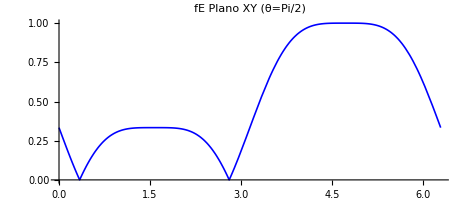

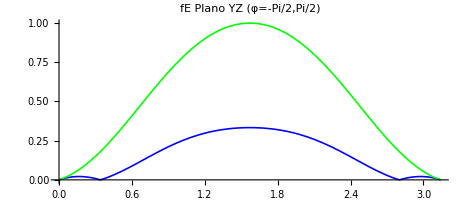

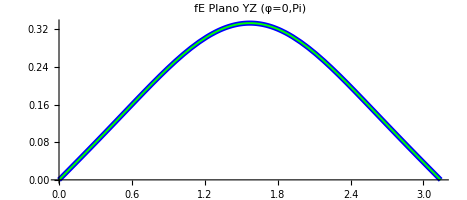

-Graphics3D-

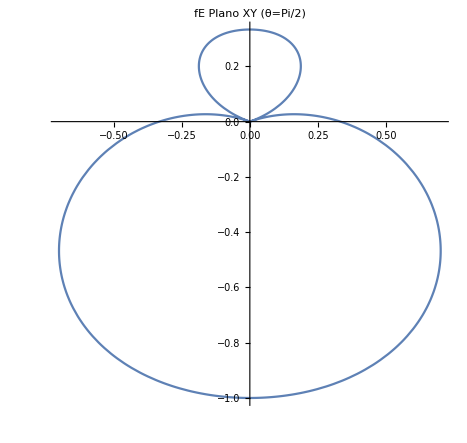

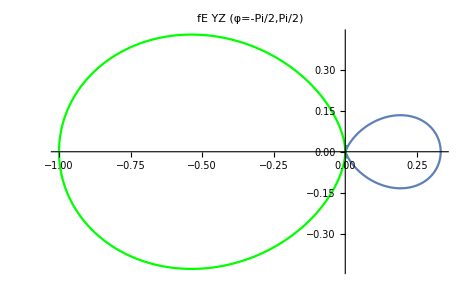

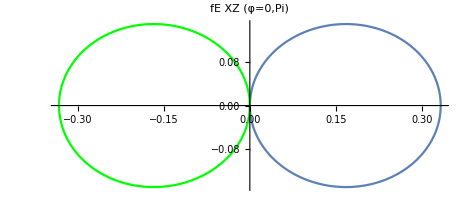

```mathematica
Clear["Global`*"]
Δ=10^-6;
fE=Function[{θ,φ},(1/3)*Abs[((Cos[Pi*Cos[θ]/2])/(Sin[θ]))*((Sin[3*Pi*(Sin[θ]*Sin[φ]+1)/4])/(Sin[Pi*(Sin[θ]*Sin[φ]+1)/4]))]];
Plot3D[fE[θ,φ],{θ,0,Pi},{φ,0,2 Pi},Axes->True,AxesLabel->{"fEx","fEy","fEz"},PlotRange->All,Mesh->30,PlotLabel->"fE",AspectRatio->Automatic]
Plot[fE[Pi/2,φ],{φ,0,2 Pi},PlotRange->All,PlotLabel->"fE Plano XY (θ=Pi/2)",PlotStyle->Directive[Blue,Thickness[0.0025]],AspectRatio->Automatic]
g1=Plot[fE[θ,Pi/2],{θ,0,Pi},PlotRange->All,PlotStyle->Directive[Blue,Thickness[0.0025]],AspectRatio->Automatic];
g2=Plot[fE[θ,-Pi/2],{θ,0,Pi},PlotRange->All,PlotStyle->Directive[Green,Thickness[0.0025]],AspectRatio->Automatic];
Show[g1,g2,PlotLabel->"fE Plano YZ (φ=-Pi/2,Pi/2)"]
g3=Plot[fE[θ,0],{θ,0,Pi},PlotRange->All,PlotStyle->Directive[Blue,Thickness[0.008]],AspectRatio->Automatic];
g4=Plot[fE[θ,Pi],{θ,0,Pi},PlotRange->All,PlotStyle->Directive[Green,Thickness[0.003]],AspectRatio->Automatic];
Show[g3,g4,PlotLabel->"fE Plano YZ (φ=0,Pi)"]
SphericalPlot3D[fE[θ,φ],{θ,0,Pi},{φ,0,2*Pi},Axes->True,AxesLabel->{"fEx","fEy","fEz"},Mesh->50,PlotRange->All,AspectRatio->Automatic]
fEx=Function[{θ,φ},fE[θ,φ]*Sin[θ]*Cos[φ]];
fEy=Function[{θ,φ},fE[θ,φ]*Sin[θ]*Sin[φ]];
fEz=Function[{θ,φ},fE[θ,φ]*Cos[θ]];
ParametricPlot[{fEx[Pi/2,φ],fEy[Pi/2,φ]},{φ,0,2*Pi},AspectRatio->Automatic,AxesLabel->"fE Plano XY (θ=Pi/2)"]
g5=ParametricPlot[{fEy[θ,Pi/2],fEz[θ,Pi/2]},{θ,0+Δ,Pi-Δ},PlotRange->All, AspectRatio->Automatic,Axes->True];
g6=ParametricPlot[{fEy[θ,-Pi/2],fEz[θ,-Pi/2]},{θ,0+Δ,Pi-Δ},AspectRatio->Automatic,PlotRange->All, Axes->True, PlotStyle->Directive[Green]];
Show[g5,g6,PlotLabel->"fE YZ (φ=-Pi/2,Pi/2)"]
g7=ParametricPlot[{fEx[θ,0],fEz[θ,0]},{θ,0+Δ,Pi-Δ},PlotRange->All, AspectRatio->Automatic,Axes->True];
g8=ParametricPlot[{fEx[θ,Pi],fEz[θ,Pi]},{θ,0+Δ,Pi-Δ},AspectRatio->Automatic,PlotRange->All, Axes->True, PlotStyle->Directive[Green]];
Show[g7,g8,PlotLabel->"fE XZ (φ=0,Pi)"]
```